```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;

ϕ=0.5 π;
ϕ3=0;

gx=0.01;
gy=0.01;

(*
(*For two middle*)
gx=0.0104;
gy=0.0104;
*)
```

```mathematica
top={};
leg={};
For[ϕ=0,ϕ≤2π,ϕ+=0.01,
gyM=0.01*Sin[ϕ];
gxM=0.01*Cos[ϕ];
(*Plus and minus gxM couple either top side to the leg*)
(*Is there a combo which uncouples the leg?  Should do an angle iteration*)
MagΔXTop=Table[gx*100*(ⅇ^((-(ii)^2)/10000)-ⅇ^((-(ii-2Nx-NxM)^2)/10000))+gxM*100*ⅇ^((-(ii-Nx-NxM/2)^2)/10000),{ii,1,2Nx+NxM}];
MagΔYTop=Table[gyM*100*ⅇ^((-(ii-Nx-NxM/2)^2)/10000),{ii,1,2Nx+NxM}];
GapTop=Table[Δ,{i,1,Length[MagΔXTop]}];
MagΔXLeg=Table[gxM*100*ⅇ^((-(ii)^2)/10000),{ii,1,Nx}];
MagΔYLeg=Table[gy*100*ⅇ^((-(ii-Nx)^2)/10000)+gyM*100*ⅇ^((-(ii)^2)/10000),{ii,1,Nx}];
GapLeg=Table[Δ,{i,1,Length[MagΔXLeg]}];
MagX1=Table[MagΔXTop[[i]],{i,1,Nx}];
MagY1=Table[MagΔYTop[[i]],{i,1,Nx}];
MagXM=Table[MagΔXTop[[i]],{i,Nx+1,Nx+NxM}];
MagYM=Table[MagΔYTop[[i]],{i,Nx+1,Nx+NxM}];
MagX2=Table[MagΔXTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagY2=Table[MagΔYTop[[i]],{i,Nx+NxM+1,2Nx+NxM}];
MagX3=MagΔXLeg;
MagY3=MagΔYLeg;
H[θM_]:=Block[{Hsp},
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY1,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->MagX1,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->MagX1,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagYM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagYM,Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->MagXM,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->MagXM,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY2,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->MagX2,Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->MagX2,Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+MagY3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-MagY3,Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ MagX3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ MagX3,Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];

Hsp
];
{e,ψ}=Transpose[Sort[Transpose[Eigensystem[H[0.],-20]]]];
n=11;
e[[n]]/Δ
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i+1-4Nx-4NxM-4Nx,Abs[ψ[[n,i]]]^2+Abs[ψ[[n,Nx+i]]]^2+Abs[ψ[[n,2Nx+i]]]^2+Abs[ψ[[n,3Nx+i]]]^2},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];
ψbar=Join[ψA1ue,ψAMue,ψA2ue];
ψleg=ψA3ue;

w=Max[Table[ψbar[[i,2]],{i,1,Length[ψbar]}]];
topi=ListPlot[{ψbar,w MagΔXTop},Joined->True,PlotRange->{-0.1,0.1}];

(*w=Max[Table[ψleg[[i,2]],{i,1,Length[ψleg]}]];*)
legi=ListPlot[{ψleg,w MagΔYLeg},Joined->True,PlotRange->{-0.1,0.1}];

top=Join[top,{topi}];
leg=Join[leg,{legi}];
Print[{ϕ,e[[11]]}]
];
```

{0,1.03513×10^-13}

{0.01,4.85216×10^-14+2.16312×10^-21 ⅈ}

{0.02,2.68252×10^-14-1.59748×10^-20 ⅈ}

{0.03,1.87025×10^-14+4.94458×10^-21 ⅈ}

{0.04,1.39466×10^-14+4.79285×10^-21 ⅈ}

{0.05,1.13427×10^-14+7.09335×10^-22 ⅈ}

{0.06,9.63422×10^-15-6.45173×10^-21 ⅈ}

{0.07,8.56316×10^-15-1.08761×10^-21 ⅈ}

{0.08,7.15779×10^-15+4.95547×10^-21 ⅈ}

{0.09,7.03555×10^-15-2.03443×10^-21 ⅈ}

{0.1,6.43092×10^-15-1.42941×10^-21 ⅈ}

{0.11,5.83371×10^-15+6.88898×10^-21 ⅈ}

{0.12,5.46981×10^-15-2.90779×10^-21 ⅈ}

{0.13,5.11029×10^-15-8.12464×10^-22 ⅈ}

{0.14,5.1825×10^-15+1.78165×10^-21 ⅈ}

{0.15,4.84641×10^-15-5.58595×10^-22 ⅈ}

{0.16,4.57449×10^-15+1.13609×10^-21 ⅈ}

{0.17,4.26327×10^-15+3.1177×10^-22 ⅈ}

{0.18,3.92972×10^-15+2.96624×10^-21 ⅈ}

{0.19,4.08727×10^-15-1.77686×10^-21 ⅈ}

{0.2,4.01421×10^-15-1.29793×10^-21 ⅈ}

{0.21,4.0042×10^-15+4.0457×10^-21 ⅈ}

{0.22,3.983×10^-15-1.62858×10^-21 ⅈ}

{0.23,3.78566×10^-15-5.89385×10^-21 ⅈ}

{0.24,3.82505×10^-15-2.05785×10^-21 ⅈ}

{0.25,3.5502×10^-15-1.32505×10^-21 ⅈ}

{0.26,3.88453×10^-15+1.19207×10^-21 ⅈ}

{0.27,4.05654×10^-15-4.17163×10^-21 ⅈ}

{0.28,3.5485×10^-15+4.60523×10^-22 ⅈ}

{0.29,3.7269×10^-15-4.10083×10^-21 ⅈ}

{0.3,3.39432×10^-15+1.86196×10^-21 ⅈ}

{0.31,3.61816×10^-15+8.60444×10^-22 ⅈ}

{0.32,4.09783×10^-15+2.24115×10^-22 ⅈ}

{0.33,3.41426×10^-15-7.41548×10^-21 ⅈ}

{0.34,3.36815×10^-15+1.31678×10^-22 ⅈ}

{0.35,3.54379×10^-15+1.41521×10^-22 ⅈ}

{0.36,3.71164×10^-15-1.5432×10^-21 ⅈ}

{0.37,3.74454×10^-15-1.11738×10^-21 ⅈ}

{0.38,3.55412×10^-15-7.80497×10^-21 ⅈ}

{0.39,3.44903×10^-15-1.00927×10^-22 ⅈ}

{0.4,3.65574×10^-15-1.97653×10^-21 ⅈ}

{0.41,3.65164×10^-15+2.35763×10^-21 ⅈ}

{0.42,3.41623×10^-15-7.23119×10^-22 ⅈ}

{0.43,3.5548×10^-15+2.56771×10^-21 ⅈ}

{0.44,3.48319×10^-15-1.89837×10^-21 ⅈ}

{0.45,3.56723×10^-15-2.69626×10^-21 ⅈ}

{0.46,3.61294×10^-15-4.74805×10^-21 ⅈ}

{0.47,3.55813×10^-15+2.96753×10^-21 ⅈ}

{0.48,3.63369×10^-15+4.45991×10^-21 ⅈ}

{0.49,3.56827×10^-15+1.34861×10^-21 ⅈ}

{0.5,3.45379×10^-15+6.86506×10^-22 ⅈ}

{0.51,3.7232×10^-15-3.93142×10^-21 ⅈ}

{0.52,3.20298×10^-15+6.85807×10^-21 ⅈ}

{0.53,3.33532×10^-15+2.48747×10^-21 ⅈ}

{0.54,3.6244×10^-15+1.2536×10^-21 ⅈ}

{0.55,3.88445×10^-15-4.46178×10^-21 ⅈ}

{0.56,3.73162×10^-15-1.08324×10^-21 ⅈ}

{0.57,3.60263×10^-15-5.37761×10^-21 ⅈ}

{0.58,3.71135×10^-15-1.61916×10^-21 ⅈ}

{0.59,3.76421×10^-15+2.56088×10^-21 ⅈ}

{0.6,3.48356×10^-15+5.9468×10^-21 ⅈ}

{0.61,3.92887×10^-15-6.56089×10^-21 ⅈ}

{0.62,3.66042×10^-15+1.58066×10^-20 ⅈ}

{0.63,3.86763×10^-15-1.0193×10^-20 ⅈ}

{0.64,3.49311×10^-15+1.59446×10^-20 ⅈ}

{0.65,3.97502×10^-15+5.70293×10^-21 ⅈ}

{0.66,3.7489×10^-15-1.76906×10^-20 ⅈ}

{0.67,4.08577×10^-15-4.07577×10^-21 ⅈ}

{0.68,4.11841×10^-15-1.93385×10^-21 ⅈ}

{0.69,3.88115×10^-15-8.58959×10^-21 ⅈ}

{0.7,3.89114×10^-15-2.66888×10^-22 ⅈ}

{0.71,4.00134×10^-15-1.35598×10^-20 ⅈ}

{0.72,3.85158×10^-15+1.34926×10^-20 ⅈ}

{0.73,3.99408×10^-15-1.14162×10^-20 ⅈ}

{0.74,3.98633×10^-15-5.53122×10^-22 ⅈ}

{0.75,4.08513×10^-15-7.31377×10^-21 ⅈ}

{0.76,4.24179×10^-15-1.05001×10^-20 ⅈ}

{0.77,4.03951×10^-15+3.3172×10^-21 ⅈ}

{0.78,4.03988×10^-15+5.53335×10^-21 ⅈ}

{0.79,4.43292×10^-15-2.69811×10^-20 ⅈ}

{0.8,4.45157×10^-15+9.72894×10^-21 ⅈ}

{0.81,4.45017×10^-15-5.91768×10^-21 ⅈ}

{0.82,4.25141×10^-15-1.57786×10^-20 ⅈ}

{0.83,4.60487×10^-15+1.05309×10^-20 ⅈ}

{0.84,4.28934×10^-15+1.46645×10^-20 ⅈ}

{0.85,4.63253×10^-15-7.22119×10^-21 ⅈ}

{0.86,4.92206×10^-15-6.70225×10^-21 ⅈ}

{0.87,5.22491×10^-15+3.4585×10^-20 ⅈ}

{0.88,4.71055×10^-15-1.34678×10^-21 ⅈ}

{0.89,5.06936×10^-15-1.73606×10^-20 ⅈ}

{0.9,5.04904×10^-15-5.94379×10^-21 ⅈ}

{0.91,4.95992×10^-15+2.20363×10^-20 ⅈ}

{0.92,5.01886×10^-15-2.56022×10^-20 ⅈ}

{0.93,5.17302×10^-15+1.09162×10^-20 ⅈ}

{0.94,5.12079×10^-15-1.12376×10^-21 ⅈ}

{0.95,5.08773×10^-15+1.18429×10^-21 ⅈ}

{0.96,5.33981×10^-15-4.08053×10^-21 ⅈ}

{0.97,5.70385×10^-15-1.40012×10^-20 ⅈ}

{0.98,5.63374×10^-15-2.67281×10^-20 ⅈ}

{0.99,5.51299×10^-15-4.32095×10^-20 ⅈ}

{1.,5.91987×10^-15+9.5826×10^-21 ⅈ}

{1.01,6.05817×10^-15+3.97553×10^-20 ⅈ}

{1.02,6.11658×10^-15+3.04289×10^-21 ⅈ}

{1.03,5.76428×10^-15-1.70242×10^-20 ⅈ}

{1.04,6.23785×10^-15+1.78481×10^-20 ⅈ}

{1.05,6.54286×10^-15+6.63855×10^-20 ⅈ}

{1.06,6.69817×10^-15-4.61823×10^-20 ⅈ}

{1.07,6.58146×10^-15+3.40327×10^-20 ⅈ}

{1.08,6.74116×10^-15+1.08876×10^-19 ⅈ}

{1.09,7.27624×10^-15+4.13951×10^-20 ⅈ}

{1.1,7.00923×10^-15+5.80664×10^-20 ⅈ}

{1.11,7.20877×10^-15-6.28854×10^-20 ⅈ}

{1.12,7.46672×10^-15+5.58256×10^-20 ⅈ}

{1.13,7.58046×10^-15+9.69585×10^-20 ⅈ}

{1.14,7.70647×10^-15+6.99305×10^-20 ⅈ}

{1.15,7.47999×10^-15+1.50582×10^-20 ⅈ}

{1.16,7.87935×10^-15-3.74652×10^-20 ⅈ}

{1.17,8.16244×10^-15+6.95844×10^-20 ⅈ}

{1.18,8.27913×10^-15+1.01286×10^-19 ⅈ}

{1.19,8.28077×10^-15+1.92585×10^-19 ⅈ}

{1.2,8.90402×10^-15+1.70934×10^-19 ⅈ}

{1.21,9.12792×10^-15-1.62975×10^-19 ⅈ}

{1.22,9.12445×10^-15+1.62484×10^-19 ⅈ}

{1.23,9.07813×10^-15-1.6481×10^-19 ⅈ}

{1.24,9.7126×10^-15+1.6838×10^-19 ⅈ}

{1.25,9.95186×10^-15-1.40467×10^-19 ⅈ}

{1.26,1.04031×10^-14-2.4957×10^-19 ⅈ}

{1.27,1.04047×10^-14+2.00327×10^-19 ⅈ}

{1.28,1.02647×10^-14+1.56304×10^-20 ⅈ}

{1.29,1.08193×10^-14+3.6574×10^-20 ⅈ}

{1.3,1.16109×10^-14-7.71398×10^-20 ⅈ}

{1.31,1.11445×10^-14-3.25556×10^-19 ⅈ}

{1.32,1.13203×10^-14+3.6417×10^-19 ⅈ}

{1.33,1.17604×10^-14-6.77586×10^-20 ⅈ}

{1.34,1.17173×10^-14+1.59285×10^-19 ⅈ}

{1.35,1.273×10^-14+1.09938×10^-19 ⅈ}

{1.36,1.28175×10^-14+4.6612×10^-19 ⅈ}

{1.37,1.30493×10^-14+2.86627×10^-19 ⅈ}

{1.38,1.29801×10^-14-6.72777×10^-20 ⅈ}

{1.39,1.3684×10^-14+4.41607×10^-19 ⅈ}

{1.4,1.39963×10^-14+4.13118×10^-20 ⅈ}

{1.41,1.42771×10^-14+2.13083×10^-19 ⅈ}

{1.42,1.49285×10^-14+2.10627×10^-19 ⅈ}

{1.43,1.44944×10^-14-2.81926×10^-19 ⅈ}

{1.44,1.50671×10^-14-2.28493×10^-19 ⅈ}

{1.45,1.52018×10^-14-2.05238×10^-19 ⅈ}

{1.46,1.53784×10^-14-3.18714×10^-19 ⅈ}

{1.47,1.57548×10^-14+7.06546×10^-20 ⅈ}

{1.48,1.54851×10^-14-4.87059×10^-19 ⅈ}

{1.49,1.55341×10^-14+5.26698×10^-20 ⅈ}

{1.5,1.57237×10^-14+1.65445×10^-19 ⅈ}

{1.51,1.58286×10^-14-5.04877×10^-19 ⅈ}

{1.52,1.57127×10^-14-1.4221×10^-19 ⅈ}

{1.53,1.59414×10^-14-1.52264×10^-19 ⅈ}

{1.54,1.54326×10^-14+4.6597×10^-21 ⅈ}

{1.55,1.54254×10^-14+8.84505×10^-21 ⅈ}

{1.56,1.52844×10^-14+5.18748×10^-20 ⅈ}

{1.57,1.51181×10^-14-3.36073×10^-21 ⅈ}

{1.58,1.49738×10^-14-3.04103×10^-19 ⅈ}

{1.59,1.48626×10^-14+6.68067×10^-21 ⅈ}

{1.6,1.44458×10^-14-2.66736×10^-19 ⅈ}

{1.61,1.41745×10^-14+1.07559×10^-19 ⅈ}

{1.62,1.36216×10^-14+5.66182×10^-19 ⅈ}

{1.63,1.35118×10^-14+3.67812×10^-19 ⅈ}

{1.64,1.33918×10^-14+4.86094×10^-19 ⅈ}

{1.65,1.26579×10^-14+8.81803×10^-19 ⅈ}

{1.66,1.23942×10^-14-2.78984×10^-21 ⅈ}

{1.67,1.2155×10^-14+2.19672×10^-19 ⅈ}

{1.68,1.18353×10^-14+4.96497×10^-19 ⅈ}

{1.69,1.12683×10^-14-5.35026×10^-19 ⅈ}

{1.7,1.10353×10^-14-1.07263×10^-18 ⅈ}

{1.71,1.07062×10^-14-1.64331×10^-18 ⅈ}

{1.72,1.02845×10^-14-1.13267×10^-18 ⅈ}

{1.73,1.02546×10^-14-4.49892×10^-19 ⅈ}

{1.74,9.81133×10^-15+7.08556×10^-19 ⅈ}

{1.75,9.60839×10^-15-8.54072×10^-19 ⅈ}

{1.76,9.2851×10^-15-3.74461×10^-18 ⅈ}

{1.77,8.69625×10^-15+2.50496×10^-18 ⅈ}

{1.78,8.41418×10^-15-1.58084×10^-18 ⅈ}

{1.79,8.31935×10^-15+3.04114×10^-18 ⅈ}

{1.8,7.97358×10^-15+1.74795×10^-18 ⅈ}

{1.81,7.82274×10^-15-6.6149×10^-19 ⅈ}

{1.82,7.31684×10^-15-1.87057×10^-18 ⅈ}

{1.83,7.20236×10^-15-2.43825×10^-19 ⅈ}

{1.84,6.92484×10^-15+2.09936×10^-18 ⅈ}

{1.85,6.88273×10^-15+1.44082×10^-18 ⅈ}

{1.86,6.69758×10^-15-5.35947×10^-18 ⅈ}

{1.87,6.57913×10^-15+6.27635×10^-19 ⅈ}

{1.88,6.1709×10^-15-6.78513×10^-19 ⅈ}

{1.89,6.11371×10^-15-2.93262×10^-18 ⅈ}

{1.9,6.0729×10^-15-5.59805×10^-18 ⅈ}

{1.91,5.69573×10^-15+7.59482×10^-21 ⅈ}

{1.92,5.43439×10^-15-1.43521×10^-17 ⅈ}

{1.93,5.48251×10^-15-2.73719×10^-18 ⅈ}

{1.94,5.08645×10^-15-8.38436×10^-18 ⅈ}

{1.95,5.27034×10^-15+9.10649×10^-18 ⅈ}

{1.96,4.76714×10^-15+7.81848×10^-18 ⅈ}

{1.97,4.97519×10^-15+4.63431×10^-18 ⅈ}

{1.98,4.78032×10^-15-9.04254×10^-18 ⅈ}

{1.99,4.71756×10^-15+1.05436×10^-17 ⅈ}

{2.,4.52488×10^-15+7.05618×10^-18 ⅈ}

{2.01,4.2425×10^-15-2.11919×10^-18 ⅈ}

{2.02,4.27205×10^-15+1.19409×10^-17 ⅈ}

{2.03,4.16487×10^-15-5.56986×10^-18 ⅈ}

{2.04,4.17597×10^-15-3.1075×10^-20 ⅈ}

{2.05,4.19821×10^-15+6.35936×10^-18 ⅈ}

{2.06,3.89367×10^-15-4.39676×10^-18 ⅈ}

{2.07,3.75285×10^-15+1.36963×10^-17 ⅈ}

{2.08,3.62484×10^-15-8.21928×10^-19 ⅈ}

{2.09,3.894×10^-15-2.32351×10^-18 ⅈ}

{2.1,3.44632×10^-15+3.3033×10^-18 ⅈ}

{2.11,3.59214×10^-15+1.10276×10^-18 ⅈ}

{2.12,3.44537×10^-15+9.59006×10^-18 ⅈ}

{2.13,3.33874×10^-15-3.35756×10^-18 ⅈ}

{2.14,3.67601×10^-15+8.91851×10^-18 ⅈ}

{2.15,3.26521×10^-15-2.86957×10^-18 ⅈ}

{2.16,3.17339×10^-15+1.48909×10^-17 ⅈ}

{2.17,3.12079×10^-15-1.04989×10^-17 ⅈ}

{2.18,3.00125×10^-15+1.70814×10^-17 ⅈ}

{2.19,2.76887×10^-15-7.19564×10^-18 ⅈ}

{2.2,3.19548×10^-15-7.35928×10^-18 ⅈ}

{2.21,3.06832×10^-15-6.75752×10^-19 ⅈ}

{2.22,2.8581×10^-15+3.65587×10^-18 ⅈ}

{2.23,2.90929×10^-15-2.11485×10^-18 ⅈ}

{2.24,2.77149×10^-15-5.80081×10^-19 ⅈ}

{2.25,2.79952×10^-15+1.24403×10^-17 ⅈ}

{2.26,3.04325×10^-15+1.43868×10^-17 ⅈ}

{2.27,2.85735×10^-15-1.02474×10^-17 ⅈ}

{2.28,2.57315×10^-15-1.6995×10^-17 ⅈ}

{2.29,2.91175×10^-15-2.88723×10^-18 ⅈ}

{2.3,2.8876×10^-15-3.39272×10^-18 ⅈ}

{2.31,2.7005×10^-15-2.68346×10^-18 ⅈ}

{2.32,2.43695×10^-15-4.35705×10^-18 ⅈ}

{2.33,2.42108×10^-15+7.20932×10^-18 ⅈ}

{2.34,2.45531×10^-15-1.12663×10^-17 ⅈ}

{2.35,2.38116×10^-15-2.89522×10^-18 ⅈ}

{2.36,2.50654×10^-15-4.60807×10^-18 ⅈ}

{2.37,2.44119×10^-15+6.96351×10^-18 ⅈ}

{2.38,2.35111×10^-15-9.09752×10^-18 ⅈ}

{2.39,2.15845×10^-15+4.49274×10^-18 ⅈ}

{2.4,2.61636×10^-15+4.76505×10^-18 ⅈ}

{2.41,2.33882×10^-15-2.52106×10^-18 ⅈ}

{2.42,2.47081×10^-15-8.68894×10^-18 ⅈ}

{2.43,2.39279×10^-15+2.75728×10^-18 ⅈ}

{2.44,2.49002×10^-15+1.34505×10^-17 ⅈ}

{2.45,2.25502×10^-15-5.24224×10^-18 ⅈ}

{2.46,2.43352×10^-15+1.24217×10^-17 ⅈ}

{2.47,2.39572×10^-15+9.9009×10^-18 ⅈ}

{2.48,2.31234×10^-15-1.36223×10^-18 ⅈ}

{2.49,2.12013×10^-15+1.28473×10^-18 ⅈ}

{2.5,2.23353×10^-15+3.45728×10^-18 ⅈ}

{2.51,2.43623×10^-15+3.03984×10^-18 ⅈ}

{2.52,2.45169×10^-15-2.6988×10^-18 ⅈ}

{2.53,2.52204×10^-15-5.76222×10^-18 ⅈ}

{2.54,2.2219×10^-15-5.16692×10^-19 ⅈ}

{2.55,2.20466×10^-15+1.35823×10^-17 ⅈ}

{2.56,2.35928×10^-15-7.25581×10^-18 ⅈ}

{2.57,2.27287×10^-15+1.89867×10^-17 ⅈ}

{2.58,2.30371×10^-15-8.16725×10^-18 ⅈ}

{2.59,2.30692×10^-15+4.59062×10^-18 ⅈ}

{2.6,1.93962×10^-15+4.26049×10^-18 ⅈ}

{2.61,2.34939×10^-15+4.12543×10^-18 ⅈ}

{2.62,2.11852×10^-15-1.20178×10^-17 ⅈ}

{2.63,2.08504×10^-15-7.96334×10^-18 ⅈ}

{2.64,2.49224×10^-15+6.00031×10^-18 ⅈ}

{2.65,2.08973×10^-15+4.53324×10^-19 ⅈ}

{2.66,2.14507×10^-15-1.40138×10^-18 ⅈ}

{2.67,2.27356×10^-15+6.50676×10^-19 ⅈ}

{2.68,2.59299×10^-15-2.08071×10^-18 ⅈ}

{2.69,2.19725×10^-15-2.77971×10^-18 ⅈ}

{2.7,2.09401×10^-15+1.36888×10^-19 ⅈ}

{2.71,2.20296×10^-15+5.12381×10^-18 ⅈ}

{2.72,2.13566×10^-15+5.37101×10^-18 ⅈ}

{2.73,2.29472×10^-15-2.04535×10^-18 ⅈ}

{2.74,2.16786×10^-15+8.65298×10^-20 ⅈ}

{2.75,2.4152×10^-15-1.54791×10^-18 ⅈ}

{2.76,2.08241×10^-15+4.22335×10^-18 ⅈ}

{2.77,2.36312×10^-15+7.52159×10^-18 ⅈ}

{2.78,2.52476×10^-15-4.24382×10^-18 ⅈ}

{2.79,2.16494×10^-15-3.63147×10^-18 ⅈ}

{2.8,2.67783×10^-15+7.44505×10^-21 ⅈ}

{2.81,2.25594×10^-15-2.54754×10^-18 ⅈ}

{2.82,2.59929×10^-15+2.87982×10^-18 ⅈ}

{2.83,2.31368×10^-15-4.99691×10^-18 ⅈ}

{2.84,2.38336×10^-15-3.74929×10^-18 ⅈ}

{2.85,2.21498×10^-15-8.97302×10^-19 ⅈ}

{2.86,2.62642×10^-15+9.32168×10^-19 ⅈ}

{2.87,2.51552×10^-15+2.47913×10^-18 ⅈ}

{2.88,2.38456×10^-15+6.31621×10^-18 ⅈ}

{2.89,2.6508×10^-15-1.1442×10^-18 ⅈ}

{2.9,2.89825×10^-15-1.26357×10^-18 ⅈ}

{2.91,2.77787×10^-15+5.89215×10^-18 ⅈ}

{2.92,3.09062×10^-15-1.30512×10^-18 ⅈ}

{2.93,3.12362×10^-15+8.77064×10^-19 ⅈ}

{2.94,2.52655×10^-15+8.8808×10^-19 ⅈ}

{2.95,2.80406×10^-15+1.92797×10^-18 ⅈ}

{2.96,3.53409×10^-15-2.98546×10^-19 ⅈ}

{2.97,2.92115×10^-15-2.785×10^-18 ⅈ}

{2.98,3.41324×10^-15-2.2811×10^-18 ⅈ}

{2.99,3.54409×10^-15+7.32693×10^-19 ⅈ}

{3.,3.82905×10^-15+1.42954×10^-18 ⅈ}

{3.01,3.83262×10^-15-8.96831×10^-19 ⅈ}

{3.02,4.15252×10^-15-8.0714×10^-19 ⅈ}

{3.03,4.46367×10^-15+1.4474×10^-18 ⅈ}

{3.04,4.78647×10^-15-4.66308×10^-19 ⅈ}

{3.05,5.52138×10^-15+1.29688×10^-18 ⅈ}

{3.06,5.80282×10^-15+2.5834×10^-19 ⅈ}

{3.07,6.64155×10^-15-2.80835×10^-19 ⅈ}

{3.08,7.07795×10^-15+2.15177×10^-18 ⅈ}

{3.09,8.81704×10^-15-1.17581×10^-18 ⅈ}

{3.1,1.05779×10^-14+5.23563×10^-19 ⅈ}

{3.11,1.34104×10^-14-1.32424×10^-19 ⅈ}

{3.12,1.95689×10^-14+2.49439×10^-19 ⅈ}

{3.13,3.54284×10^-14-1.08813×10^-19 ⅈ}

{3.14,2.55468×10^-13+1.807×10^-20 ⅈ}

{3.15,3.94558×10^-14+1.16076×10^-19 ⅈ}

{3.16,1.88139×10^-14+1.25091×10^-19 ⅈ}

{3.17,1.2107×10^-14+8.31962×10^-21 ⅈ}

{3.18,9.6669×10^-15+6.87472×10^-20 ⅈ}

{3.19,7.71698×10^-15+2.53782×10^-19 ⅈ}

{3.2,7.02586×10^-15+1.58903×10^-19 ⅈ}

{3.21,6.06334×10^-15-1.5116×10^-19 ⅈ}

{3.22,5.52159×10^-15-8.45897×10^-19 ⅈ}

{3.23,5.38863×10^-15-9.59127×10^-19 ⅈ}

{3.24,5.11611×10^-15-2.41321×10^-18 ⅈ}

{3.25,4.21645×10^-15+2.57247×10^-19 ⅈ}

{3.26,4.33244×10^-15-1.20663×10^-19 ⅈ}

{3.27,3.91439×10^-15-5.74895×10^-19 ⅈ}

{3.28,4.19799×10^-15-1.37775×10^-18 ⅈ}

{3.29,3.87712×10^-15+5.02183×10^-19 ⅈ}

{3.3,3.52735×10^-15-1.0675×10^-19 ⅈ}

{3.31,4.19863×10^-15+3.71357×10^-19 ⅈ}

{3.32,3.72047×10^-15+7.97025×10^-19 ⅈ}

{3.33,3.46732×10^-15-1.55012×10^-19 ⅈ}

{3.34,3.50243×10^-15+2.61876×10^-18 ⅈ}

{3.35,3.42577×10^-15+3.15102×10^-19 ⅈ}

{3.36,3.40879×10^-15-1.22961×10^-18 ⅈ}

{3.37,3.46289×10^-15-2.72314×10^-18 ⅈ}

{3.38,3.64004×10^-15-1.25534×10^-18 ⅈ}

{3.39,3.4835×10^-15+9.69602×10^-19 ⅈ}

{3.4,3.35932×10^-15-2.61696×10^-18 ⅈ}

{3.41,3.42003×10^-15-1.04641×10^-17 ⅈ}

{3.42,3.3129×10^-15-1.80482×10^-18 ⅈ}

{3.43,3.59703×10^-15+5.12563×10^-18 ⅈ}

{3.44,3.48064×10^-15-5.22977×10^-18 ⅈ}

{3.45,3.49789×10^-15+4.67014×10^-18 ⅈ}

{3.46,3.61249×10^-15-3.00209×10^-18 ⅈ}

{3.47,3.75926×10^-15-5.94725×10^-18 ⅈ}

{3.48,3.62444×10^-15+7.15764×10^-20 ⅈ}

{3.49,3.99643×10^-15-5.29976×10^-18 ⅈ}

{3.5,3.9127×10^-15-1.67443×10^-18 ⅈ}

{3.51,3.81955×10^-15-3.39047×10^-18 ⅈ}

{3.52,4.2945×10^-15-4.79005×10^-18 ⅈ}

{3.53,4.00052×10^-15+4.62439×10^-18 ⅈ}

{3.54,4.20853×10^-15+1.4347×10^-18 ⅈ}

{3.55,4.21058×10^-15+3.36861×10^-18 ⅈ}

{3.56,4.48019×10^-15-3.86144×10^-18 ⅈ}

{3.57,4.54672×10^-15+1.28444×10^-18 ⅈ}

{3.58,4.69071×10^-15+1.24649×10^-18 ⅈ}

{3.59,4.62951×10^-15-7.64158×10^-18 ⅈ}

{3.6,4.42702×10^-15-2.7181×10^-18 ⅈ}

{3.61,4.70192×10^-15-6.35748×10^-18 ⅈ}

{3.62,4.85358×10^-15+6.09385×10^-18 ⅈ}

{3.63,5.23692×10^-15+6.14144×10^-18 ⅈ}

{3.64,5.22467×10^-15-4.67003×10^-18 ⅈ}

{3.65,5.15833×10^-15-2.77361×10^-18 ⅈ}

{3.66,5.68261×10^-15+7.37256×10^-19 ⅈ}

{3.67,5.69038×10^-15+1.07248×10^-18 ⅈ}

{3.68,6.28284×10^-15-1.09515×10^-18 ⅈ}

{3.69,6.01044×10^-15+5.40116×10^-18 ⅈ}

{3.7,6.11343×10^-15-3.44406×10^-18 ⅈ}

{3.71,6.28995×10^-15+4.93711×10^-18 ⅈ}

{3.72,6.88169×10^-15+7.85541×10^-19 ⅈ}

{3.73,7.07769×10^-15-1.50895×10^-18 ⅈ}

{3.74,7.31995×10^-15-9.43727×10^-18 ⅈ}

{3.75,8.08402×10^-15+5.14858×10^-18 ⅈ}

{3.76,7.81772×10^-15-1.44383×10^-19 ⅈ}

{3.77,8.35728×10^-15-2.85389×10^-18 ⅈ}

{3.78,8.73207×10^-15+8.34522×10^-18 ⅈ}

{3.79,8.90403×10^-15-8.99293×10^-19 ⅈ}

{3.8,9.5225×10^-15-4.31385×10^-18 ⅈ}

{3.81,9.97085×10^-15+8.25528×10^-19 ⅈ}

{3.82,1.01651×10^-14+2.94375×10^-18 ⅈ}

{3.83,1.06898×10^-14+9.1496×10^-18 ⅈ}

{3.84,1.09313×10^-14+2.81998×10^-18 ⅈ}

{3.85,1.18794×10^-14+2.4025×10^-18 ⅈ}

{3.86,1.20652×10^-14-5.33827×10^-18 ⅈ}

{3.87,1.24846×10^-14+1.16358×10^-17 ⅈ}

{3.88,1.2989×10^-14+5.57269×10^-19 ⅈ}

{3.89,1.40945×10^-14+1.80379×10^-18 ⅈ}

{3.9,1.45606×10^-14+9.79279×10^-18 ⅈ}

{3.91,1.53812×10^-14+1.95194×10^-17 ⅈ}

{3.92,1.56649×10^-14+7.69325×10^-18 ⅈ}

{3.93,1.66018×10^-14-5.92593×10^-18 ⅈ}

{3.94,1.7154×10^-14+8.3324×10^-18 ⅈ}

{3.95,1.80191×10^-14+6.1236×10^-18 ⅈ}

{3.96,1.92063×10^-14-2.33839×10^-18 ⅈ}

{3.97,1.94552×10^-14-1.43125×10^-17 ⅈ}

{3.98,2.06283×10^-14+3.01886×10^-18 ⅈ}

{3.99,2.18039×10^-14+5.36477×10^-18 ⅈ}

{4.,2.27112×10^-14-2.1898×10^-17 ⅈ}

{4.01,2.38048×10^-14-4.60565×10^-18 ⅈ}

{4.02,2.48516×10^-14+6.58764×10^-18 ⅈ}

{4.03,2.62962×10^-14+6.53746×10^-17 ⅈ}

{4.04,2.79818×10^-14-4.50077×10^-17 ⅈ}

{4.05,2.88757×10^-14+4.38054×10^-18 ⅈ}

{4.06,3.05162×10^-14+7.2509×10^-18 ⅈ}

{4.07,3.18886×10^-14+3.5403×10^-18 ⅈ}

{4.08,3.35665×10^-14+4.079×10^-18 ⅈ}

{4.09,3.53625×10^-14-4.86444×10^-18 ⅈ}

{4.1,3.70571×10^-14-7.95098×10^-19 ⅈ}

{4.11,3.9329×10^-14+5.73314×10^-17 ⅈ}

{4.12,4.14192×10^-14+7.74398×10^-17 ⅈ}

{4.13,4.39087×10^-14+3.65661×10^-18 ⅈ}

{4.14,4.62675×10^-14-1.92203×10^-17 ⅈ}

{4.15,4.87747×10^-14+8.40338×10^-18 ⅈ}

{4.16,5.16063×10^-14-1.80142×10^-17 ⅈ}

{4.17,5.47809×10^-14+1.53942×10^-17 ⅈ}

{4.18,5.76505×10^-14+2.23163×10^-17 ⅈ}

{4.19,6.13309×10^-14-8.62935×10^-18 ⅈ}

{4.2,6.50204×10^-14+1.03357×10^-17 ⅈ}

{4.21,6.91011×10^-14+1.60028×10^-17 ⅈ}

{4.22,7.29684×10^-14-1.35628×10^-17 ⅈ}

{4.23,7.79945×10^-14-2.9085×10^-18 ⅈ}

{4.24,8.31115×10^-14+4.79239×10^-18 ⅈ}

{4.25,8.77573×10^-14+7.52148×10^-18 ⅈ}

{4.26,9.38226×10^-14+1.23672×10^-17 ⅈ}

{4.27,1.00067×10^-13-4.41766×10^-18 ⅈ}

{4.28,1.06409×10^-13-6.33957×10^-18 ⅈ}

{4.29,1.13777×10^-13+1.01477×10^-17 ⅈ}

{4.3,1.21125×10^-13-4.70799×10^-18 ⅈ}

{4.31,1.29879×10^-13+6.75312×10^-18 ⅈ}

{4.32,1.3892×10^-13+3.28558×10^-18 ⅈ}

{4.33,1.48228×10^-13-1.14598×10^-17 ⅈ}

{4.34,1.58693×10^-13-4.28086×10^-18 ⅈ}

{4.35,1.70165×10^-13+9.53706×10^-18 ⅈ}

{4.36,1.82628×10^-13-1.35033×10^-18 ⅈ}

{4.37,1.95959×10^-13-7.07162×10^-18 ⅈ}

{4.38,2.10302×10^-13-8.49364×10^-20 ⅈ}

{4.39,2.26046×10^-13+5.94226×10^-19 ⅈ}

{4.4,2.42845×10^-13-3.3951×10^-18 ⅈ}

{4.41,2.60897×10^-13+2.62781×10^-19 ⅈ}

{4.42,2.8084×10^-13+2.91783×10^-18 ⅈ}

{4.43,3.01663×10^-13-7.14921×10^-18 ⅈ}

{4.44,3.24689×10^-13+1.17782×10^-18 ⅈ}

{4.45,3.49929×10^-13+1.00033×10^-18 ⅈ}

{4.46,3.76279×10^-13-8.59953×10^-18 ⅈ}

{4.47,4.04992×10^-13+3.03856×10^-18 ⅈ}

{4.48,4.35215×10^-13-1.17622×10^-18 ⅈ}

{4.49,4.67663×10^-13-1.78184×10^-18 ⅈ}

{4.5,5.02218×10^-13+3.35725×10^-19 ⅈ}

{4.51,5.38247×10^-13-8.22263×10^-19 ⅈ}

{4.52,5.75647×10^-13-6.44253×10^-19 ⅈ}

{4.53,6.1467×10^-13-4.1122×10^-18 ⅈ}

{4.54,6.54337×10^-13-4.85126×10^-18 ⅈ}

{4.55,6.94196×10^-13-1.28901×10^-18 ⅈ}

{4.56,7.34012×10^-13+1.01129×10^-18 ⅈ}

{4.57,7.7315×10^-13+1.36708×10^-18 ⅈ}

{4.58,8.10379×10^-13-1.61615×10^-18 ⅈ}

{4.59,8.46212×10^-13+1.56528×10^-18 ⅈ}

{4.6,8.79249×10^-13+8.91706×10^-19 ⅈ}

{4.61,9.09528×10^-13-6.5215×10^-20 ⅈ}

{4.62,9.36091×10^-13+1.32623×10^-18 ⅈ}

{4.63,9.59726×10^-13-1.27526×10^-18 ⅈ}

{4.64,9.80227×10^-13-1.69368×10^-18 ⅈ}

{4.65,9.97252×10^-13-7.11036×10^-19 ⅈ}

{4.66,1.01165×10^-12-7.87045×10^-20 ⅈ}

{4.67,1.02303×10^-12+5.5023×10^-19 ⅈ}

{4.68,1.0325×10^-12+6.8387×10^-19 ⅈ}

{4.69,1.04016×10^-12-4.3666×10^-19 ⅈ}

{4.7,1.04692×10^-12-1.12178×10^-19 ⅈ}

{4.71,1.05205×10^-12+4.46624×10^-20 ⅈ}

{4.72,1.05639×10^-12+8.33107×10^-20 ⅈ}

{4.73,1.06067×10^-12+1.01904×10^-19 ⅈ}

{4.74,1.06444×10^-12-3.68175×10^-19 ⅈ}

{4.75,1.06876×10^-12+3.95436×10^-19 ⅈ}

{4.76,1.07319×10^-12-6.79702×10^-19 ⅈ}

{4.77,1.07824×10^-12+3.0518×10^-19 ⅈ}

{4.78,1.08367×10^-12+4.43626×10^-19 ⅈ}

{4.79,1.08959×10^-12+6.41698×10^-19 ⅈ}

{4.8,1.0961×10^-12-7.83628×10^-20 ⅈ}

{4.81,1.10396×10^-12-5.10399×10^-19 ⅈ}

{4.82,1.11207×10^-12+4.80282×10^-19 ⅈ}

{4.83,1.12156×10^-12-1.73043×10^-18 ⅈ}

{4.84,1.13084×10^-12+3.11075×10^-19 ⅈ}

{4.85,1.14066×10^-12-1.48691×10^-18 ⅈ}

{4.86,1.15114×10^-12+1.31613×10^-18 ⅈ}

{4.87,1.16101×10^-12-1.73068×10^-18 ⅈ}

{4.88,1.17081×10^-12-1.66411×10^-19 ⅈ}

{4.89,1.17879×10^-12+1.61789×10^-18 ⅈ}

{4.9,1.18584×10^-12-3.80307×10^-19 ⅈ}

{4.91,1.18966×10^-12+3.67792×10^-19 ⅈ}

{4.92,1.19064×10^-12-3.02517×10^-19 ⅈ}

{4.93,1.18758×10^-12+3.80557×10^-20 ⅈ}

{4.94,1.17958×10^-12-4.91918×10^-19 ⅈ}

{4.95,1.16641×10^-12-1.52784×10^-19 ⅈ}

{4.96,1.1474×10^-12-2.3205×10^-19 ⅈ}

{4.97,1.12459×10^-12+3.03526×10^-19 ⅈ}

{4.98,1.09609×10^-12+3.62038×10^-20 ⅈ}

{4.99,1.06306×10^-12}

{5.,1.02729×10^-12}

{5.01,9.87943×10^-13-5.53454×10^-20 ⅈ}

{5.02,9.48482×10^-13-1.81419×10^-19 ⅈ}

{5.03,9.07889×10^-13-1.45962×10^-20 ⅈ}

{5.04,8.68102×10^-13-3.51852×10^-19 ⅈ}

{5.05,8.28989×10^-13+3.88115×10^-20 ⅈ}

{5.06,7.91194×10^-13-2.40326×10^-19 ⅈ}

{5.07,7.5528×10^-13+9.71952×10^-20 ⅈ}

{5.08,7.20859×10^-13-3.22839×10^-19 ⅈ}

{5.09,6.88744×10^-13-2.59542×10^-19 ⅈ}

{5.1,6.59045×10^-13+1.94292×10^-18 ⅈ}

{5.11,6.31021×10^-13-1.49675×10^-18 ⅈ}

{5.12,6.05311×10^-13+6.07802×10^-19 ⅈ}

{5.13,5.81589×10^-13+1.2704×10^-18 ⅈ}

{5.14,5.59367×10^-13-2.2833×10^-18 ⅈ}

{5.15,5.38855×10^-13-1.09371×10^-18 ⅈ}

{5.16,5.19952×10^-13-3.93861×10^-18 ⅈ}

{5.17,5.02984×10^-13+4.70344×10^-19 ⅈ}

{5.18,4.87031×10^-13+4.53217×10^-18 ⅈ}

{5.19,4.72661×10^-13-6.09811×10^-18 ⅈ}

{5.2,4.59051×10^-13+3.36876×10^-18 ⅈ}

{5.21,4.46971×10^-13+7.92508×10^-18 ⅈ}

{5.22,4.35802×10^-13-1.29164×10^-19 ⅈ}

{5.23,4.25244×10^-13+7.2574×10^-19 ⅈ}

{5.24,4.15932×10^-13+1.67176×10^-18 ⅈ}

{5.25,4.07137×10^-13+3.83932×10^-18 ⅈ}

{5.26,3.99084×10^-13-3.86199×10^-18 ⅈ}

{5.27,3.91609×10^-13+2.83173×10^-18 ⅈ}

{5.28,3.84532×10^-13-4.82158×10^-19 ⅈ}

{5.29,3.78714×10^-13+2.16494×10^-18 ⅈ}

{5.3,3.725×10^-13+2.46104×10^-18 ⅈ}

{5.31,3.67138×10^-13+1.95688×10^-18 ⅈ}

{5.32,3.6252×10^-13+2.17713×10^-18 ⅈ}

{5.33,3.57922×10^-13+2.39398×10^-18 ⅈ}

{5.34,3.53643×10^-13-1.01323×10^-17 ⅈ}

{5.35,3.4961×10^-13-2.81211×10^-18 ⅈ}

{5.36,3.45731×10^-13-4.35849×10^-18 ⅈ}

{5.37,3.4252×10^-13-2.75971×10^-18 ⅈ}

{5.38,3.39133×10^-13-1.45539×10^-18 ⅈ}

{5.39,3.35945×10^-13-3.40237×10^-18 ⅈ}

{5.4,3.3327×10^-13-4.11566×10^-18 ⅈ}

{5.41,3.30347×10^-13+7.83262×10^-18 ⅈ}

{5.42,3.27953×10^-13-5.07141×10^-18 ⅈ}

{5.43,3.2512×10^-13-3.17757×10^-18 ⅈ}

{5.44,3.22885×10^-13+8.10432×10^-18 ⅈ}

{5.45,3.20643×10^-13+2.91829×10^-18 ⅈ}

{5.46,3.18601×10^-13+1.09437×10^-17 ⅈ}

{5.47,3.1627×10^-13+4.40225×10^-18 ⅈ}

{5.48,3.14183×10^-13-2.20262×10^-18 ⅈ}

{5.49,3.12123×10^-13+1.52906×10^-18 ⅈ}

{5.5,3.10296×10^-13-6.12052×10^-18 ⅈ}

{5.51,3.08232×10^-13-7.13749×10^-18 ⅈ}

{5.52,3.06361×10^-13-1.63834×10^-17 ⅈ}

{5.53,3.04647×10^-13+5.9291×10^-18 ⅈ}

{5.54,3.02621×10^-13-3.32523×10^-19 ⅈ}

{5.55,3.00818×10^-13-8.18846×10^-19 ⅈ}

{5.56,2.99091×10^-13+4.45112×10^-18 ⅈ}

{5.57,2.96814×10^-13+1.35391×10^-17 ⅈ}

{5.58,2.94616×10^-13-7.50864×10^-18 ⅈ}

{5.59,2.91427×10^-13+1.14207×10^-17 ⅈ}

{5.6,2.88272×10^-13+8.26444×10^-19 ⅈ}

{5.61,2.84169×10^-13+2.62292×10^-18 ⅈ}

{5.62,2.79178×10^-13+4.39478×10^-19 ⅈ}

{5.63,2.72979×10^-13-1.73353×10^-18 ⅈ}

{5.64,2.64745×10^-13+4.21996×10^-18 ⅈ}

{5.65,2.55524×10^-13-9.6997×10^-18 ⅈ}

{5.66,2.43441×10^-13+5.27923×10^-18 ⅈ}

{5.67,2.28135×10^-13+1.36206×10^-17 ⅈ}

{5.68,2.10277×10^-13-1.36968×10^-18 ⅈ}

{5.69,1.89916×10^-13-6.15579×10^-19 ⅈ}

{5.7,1.66961×10^-13+3.8746×10^-18 ⅈ}

{5.71,1.43169×10^-13-2.68157×10^-18 ⅈ}

{5.72,1.20034×10^-13+2.48357×10^-19 ⅈ}

{5.73,9.88541×10^-14+3.28511×10^-18 ⅈ}

{5.74,7.99107×10^-14-5.06662×10^-19 ⅈ}

{5.75,6.52837×10^-14+4.96362×10^-18 ⅈ}

{5.76,5.35755×10^-14+4.72054×10^-19 ⅈ}

{5.77,4.42108×10^-14-7.43837×10^-19 ⅈ}

{5.78,3.71199×10^-14+4.39577×10^-20 ⅈ}

{5.79,3.23511×10^-14-1.30799×10^-18 ⅈ}

{5.8,2.76178×10^-14+1.77548×10^-19 ⅈ}

{5.81,2.4042×10^-14+1.60356×10^-20 ⅈ}

{5.82,2.18328×10^-14-8.71805×10^-20 ⅈ}

{5.83,1.918×10^-14+2.88035×10^-19 ⅈ}

{5.84,1.79178×10^-14-4.13917×10^-19 ⅈ}

{5.85,1.65082×10^-14-3.43947×10^-19 ⅈ}

{5.86,1.50543×10^-14-5.42641×10^-20 ⅈ}

{5.87,1.35113×10^-14+8.28824×10^-20 ⅈ}

{5.88,1.30398×10^-14-4.93267×10^-20 ⅈ}

{5.89,1.21809×10^-14-2.49061×10^-20 ⅈ}

{5.9,1.14913×10^-14+3.75878×10^-20 ⅈ}

{5.91,1.08462×10^-14-1.36358×10^-20 ⅈ}

{5.92,1.05397×10^-14-2.71615×10^-21 ⅈ}

{5.93,9.64671×10^-15+1.43321×10^-20 ⅈ}

{5.94,9.1782×10^-15-4.39514×10^-21 ⅈ}

{5.95,9.33639×10^-15+7.02491×10^-21 ⅈ}

{5.96,9.02832×10^-15-4.41621×10^-21 ⅈ}

{5.97,8.11391×10^-15+2.91401×10^-20 ⅈ}

{5.98,8.2455×10^-15+1.99545×10^-20 ⅈ}

{5.99,7.62163×10^-15+1.80635×10^-20 ⅈ}

{6.,7.52349×10^-15-6.76666×10^-21 ⅈ}

{6.01,7.3749×10^-15-1.60308×10^-20 ⅈ}

{6.02,7.14427×10^-15-2.36249×10^-20 ⅈ}

{6.03,7.28958×10^-15+1.2362×10^-21 ⅈ}

{6.04,6.8635×10^-15+2.03705×10^-20 ⅈ}

{6.05,6.92258×10^-15-1.17482×10^-20 ⅈ}

{6.06,6.58463×10^-15-2.08373×10^-20 ⅈ}

{6.07,6.8951×10^-15+2.18107×10^-20 ⅈ}

{6.08,6.74834×10^-15+7.20821×10^-21 ⅈ}

{6.09,7.07907×10^-15-1.23294×10^-20 ⅈ}

{6.1,6.82704×10^-15+5.41103×10^-21 ⅈ}

{6.11,6.6833×10^-15+6.73769×10^-22 ⅈ}

{6.12,6.93815×10^-15+5.76476×10^-21 ⅈ}

{6.13,6.94291×10^-15+1.562×10^-22 ⅈ}

{6.14,7.18221×10^-15+1.03388×10^-21 ⅈ}

{6.15,6.91225×10^-15-1.02554×10^-20 ⅈ}

{6.16,7.40703×10^-15+3.87997×10^-21 ⅈ}

{6.17,8.10801×10^-15+1.13066×10^-20 ⅈ}

{6.18,8.56927×10^-15-1.45819×10^-20 ⅈ}

{6.19,8.55788×10^-15+4.50152×10^-21 ⅈ}

{6.2,8.99762×10^-15-3.93394×10^-21 ⅈ}

{6.21,1.00042×10^-14-2.31212×10^-21 ⅈ}

{6.22,1.12029×10^-14+8.60047×10^-21 ⅈ}

{6.23,1.26577×10^-14-5.60616×10^-21 ⅈ}

{6.24,1.5484×10^-14+1.41667×10^-21 ⅈ}

{6.25,1.92678×10^-14-3.46648×10^-21 ⅈ}

{6.26,2.56822×10^-14-5.17928×10^-21 ⅈ}

{6.27,4.26738×10^-14+2.04183×10^-20 ⅈ}

{6.28,9.16756×10^-14+2.18498×10^-20 ⅈ}

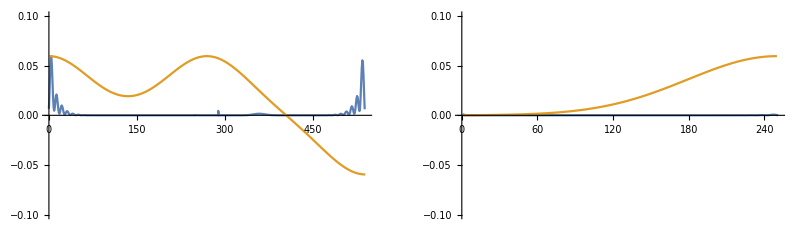

```mathematica
i=1;
GraphicsRow[{top[[i]],leg[[i]]}]
```

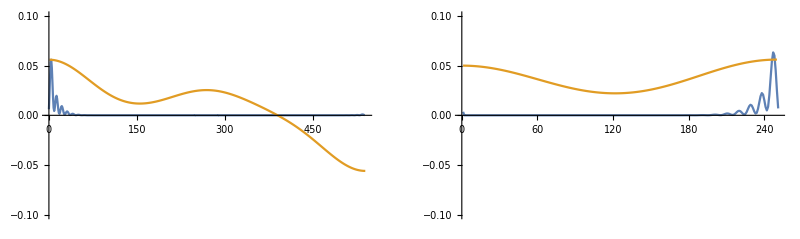

```mathematica
i=111;
GraphicsRow[{top[[i]],leg[[i]]}]
```

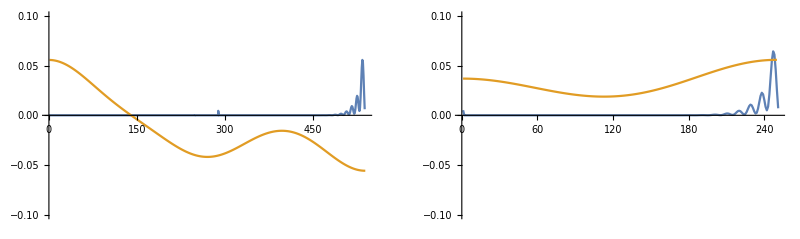

```mathematica
i=243;
GraphicsRow[{top[[i]],leg[[i]]}]
```

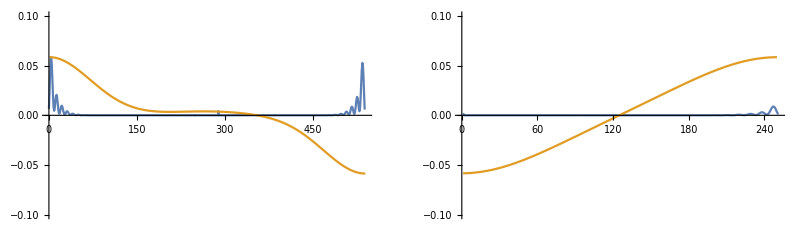

```mathematica
i=479;
GraphicsRow[{top[[i]],leg[[i]]}]
```

```mathematica
Manipulate[GraphicsRow[{top[[i]],leg[[i]]}],{i,1,Length[top],1}]
```